```mathematica
ClearAll["Global`*"]
```

```mathematica
SetOptions[EvaluationNotebook[],Background->LightGray]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/D"];
```

```mathematica
data=Import[#,"Table"]&/@FileNames["eval*"];
```

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
```

```mathematica
Do[ReEv[i]=Table[vec[i][[j,1]],{j,1,Length[vec[i]]}],{i,1,Length[data]}]
```

```mathematica
Do[SortReEv1[i]=Drop[Sort[ReEv[i]],-1],{i,1,Length[data]}]
```

```mathematica
Do[SortReEv2[i]=Drop[Sort[ReEv[i]],-2],{i,1,Length[data]}]
```

```mathematica
Do[MaxEv[i]=Max[ReEv[i]],{i,1,Length[data]}]
```

```mathematica
Do[MaxEv1[i]=Max[SortReEv1[i]],{i,1,Length[data]}]
```

```mathematica
Do[MaxEv2[i]=Max[SortReEv2[i]],{i,1,Length[data]}]
```

```mathematica
xs=Table[i*0.08,{i,1,Length[data]}];
ys=Table[MaxEv[i],{i,1,Length[data]}];
ys1=Table[MaxEv1[i],{i,1,Length[data]}];
ys2=Table[MaxEv2[i],{i,1,Length[data]}];
pairs=Thread[{xs,ys}];
pairs1=Thread[{xs,ys1/1}];
pairs2=Thread[{xs,ys2}];
```

```mathematica
l1=ListPlot[pairs,Joined->False,PlotRange->All,PlotStyle->{PointSize[0.01],Red},AxesLabel->{"mu1/mu2","s"},LabelStyle->Directive[14]];
```

```mathematica
pairs1
```

{{0.08,1.05826×10^-11},{0.16,-0.0227052242614147019},{0.24,-0.0280887203925537024},{0.32,-0.0243486197134225139},{0.4,-0.0196651849979434627},{0.48,-0.0155489543693612103},{0.56,-0.0135482918385044868},{0.64,-0.0068689595812107757},{0.72,-3.45655×10^-12},{0.8,6.44448×10^-13},{0.88,1.41236×10^-12},{0.96,-1.24351×10^-12},{1.04,-0.000428676},{1.12,-0.0012125708902107502},{1.2,-0.0018860569968344473},{1.28,-0.0024533813922719703},{1.36,-0.0029265758557116615},{1.44,-0.0033190316460740559},{1.52,-0.0036432258052286471},{1.6,-0.0039100409019583639},{1.68,-0.0041286970205479797},{1.76,-0.0043069038023278439},{1.84,-0.0044510737790052109},{1.92,-0.0045665344365985183},{2.,-0.0046577168454789751},{2.08,-0.0047283153433106857},{2.16,-0.004781419559848071},{2.24,-0.0048196222623887687},{2.32,-0.004845106987257969},{2.4,-0.0048597191609926682},{2.48,-0.004865023821905015},{2.56,-0.0048623526270706111},{2.64,-0.0048528421943552285},{2.72,-0.004837465519639747},{2.8,-0.0048170578095020405},{2.88,-0.0047923378013719972},{2.96,-0.0047639254350174132},{3.04,-0.0047323565660001496},{3.12,-0.0046980952397198553},{3.2,-0.0046615440147467881},{3.28,-0.0046230526096943062},{3.36,-0.0045829252748899475},{3.44,-0.0045414269528592493},{3.52,-0.0044987886121489852},{3.6,-0.0044552117234968906},{3.68,-0.0044108721323419748},{3.76,-0.0043659233786677984},{3.84,-0.0043204995342058196},{3.92,-0.0042747176494596153},{4.,-0.0042286799446865659},{4.08,-0.0041824756022118522},{4.16,-0.004136182374657865},{4.24,-0.0040898679735978331},{4.32,-0.0040435913040049029},{4.4,-0.0039974035362409979},{4.48,-0.0039513490226395428},{4.56,-0.0039054661143071629},{4.64,-0.0038597878756406918},{4.72,-0.0038143427186936498},{4.8,-0.0037691549602217119},{4.88,-0.0037242452980351258},{4.96,-0.0036796312581216378},{5.04,-0.0036353275621682302},{5.12,-0.0035913464564948381},{5.2,-0.0035476980368895957},{5.28,-0.0035043904698119671},{5.36,-0.0034614302710779484},{5.44,-0.0034188224654818794},{5.52,-0.0033765708108404969},{5.6,-0.0033346779253113175},{5.68,-0.0032931454509958942},{5.76,-0.0032519741492435883},{5.84,-0.003211164090389209},{5.92,-0.003170714656067183},{6.,-0.0031306246824581024},{6.08,-0.0030908925320842005},{6.16,-0.0030515161516030372},{6.24,-0.0030124931516741517},{6.32,-0.0029738208096551756},{6.4,-0.0029354962202086049},{6.48,-0.0028975162103863561},{6.56,-0.0028598774767515317},{6.64,-0.002822576570232117},{6.72,-0.0027856099273802786},{6.8,-0.0027489739205656168},{6.88,-0.0027126648260159644},{6.96,-0.0026766789262266878},{7.04,-0.0026410124595312415},{7.12,-0.0026056616359928161},{7.2,-0.0025706226908054301},{7.28,-0.0025358918783016889},{7.36,-0.0025014654555275979},{7.44,-0.0024673397265716928},{7.52,-0.0024335110221767463},{7.6,-0.0023999757222157286},{7.68,-0.0023667302573973817},{7.76,-0.0023337711029868934},{7.84,-0.0023010947953884583},{7.92,-0.0022686979298962759},{8.,-0.0022365771461745742}}

```mathematica
l3=ListPlot[pairs1,Joined->False,PlotRange->{{1,8},{-.007,0}},PlotStyle->{PointSize[0.01],Orange},AxesLabel->{"mu1/mu2","s"},LabelStyle->Directive[14]]
```

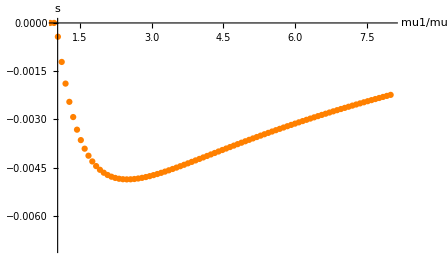

```mathematica
l2=ListPlot[pairs2,Joined->False,PlotRange->All,PlotStyle->{PointSize[0.01],Blue},AxesLabel->{"mu1/mu2","s"},LabelStyle->Directive[14]];
```

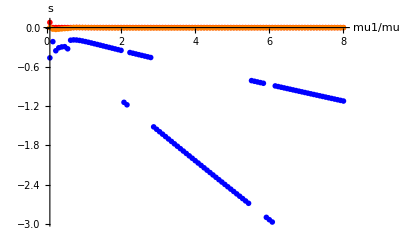

```mathematica
Show[l1,l2,l3,PlotRange->All]
```

```mathematica
SetDirectory["/Users/spencerbryngelson/Desktop/Fortran/EV_Spectral/V"]
```

/Users/spencerbryngelson/Desktop/Fortran/EV_spectral/V

```mathematica
ClearAll["Global`*"]
```

```mathematica
data=Import[#,"Table"]&/@FileNames["x.*"];
```

```mathematica
vec[1];
```

```mathematica
Length[data]
```

270

```mathematica
Table[vec[j]=data[[j]],{j,1,Length[data]}];
Table[realvec[i]=Table[vec[i][[j,1]],{j,1,Length[data]}],{i,1,Length[data]}];
Table[imvec[i]=Table[vec[i][[j,2]],{j,1,Length[data]}],{i,1,Length[data]}];
```

Part::partw: Part 169 of {{4.8255×10^-14, 3.28766×10^-15}, {1.81828×10^-14, 1.19801×10^-15}, {1.17019×10^-14, 7.6876×10^-16}, {2.05297×10^-14, 1.36315×10^-15}, {3.20585×10^-14, 2.12459×10^-15}, {5.04885×10^-14, 3.3465×10^-15}, {7.28146×10^-14, 4.82294×10^-15}, {9.75582×10^-14, 6.46136×10^-15}, {1.24375×10^-13, 8.23477×10^-15}, « 33 », {-9.62583×10^-14, 1.45425×10^-12}, {-9.74889×10^-14, 1.47285×10^-12}, {-9.88289×10^-14, 1.4931×10^-12}, {-1.00239×10^-13, 1.51441×10^-12}, {-1.0171×10^-13, 1.53664×10^-12}, {-1.0318×10^-13, 1.55885×10^-12}, {-1.04619×10^-13, 1.5806×10^-12}, {-1.05983×10^-13, 1.60122×10^-12}, « 118 »} does not exist.

Part::partw: Part 170 of {{4.8255×10^-14, 3.28766×10^-15}, {1.81828×10^-14, 1.19801×10^-15}, {1.17019×10^-14, 7.6876×10^-16}, {2.05297×10^-14, 1.36315×10^-15}, {3.20585×10^-14, 2.12459×10^-15}, {5.04885×10^-14, 3.3465×10^-15}, {7.28146×10^-14, 4.82294×10^-15}, {9.75582×10^-14, 6.46136×10^-15}, {1.24375×10^-13, 8.23477×10^-15}, « 33 », {-9.62583×10^-14, 1.45425×10^-12}, {-9.74889×10^-14, 1.47285×10^-12}, {-9.88289×10^-14, 1.4931×10^-12}, {-1.00239×10^-13, 1.51441×10^-12}, {-1.0171×10^-13, 1.53664×10^-12}, {-1.0318×10^-13, 1.55885×10^-12}, {-1.04619×10^-13, 1.5806×10^-12}, {-1.05983×10^-13, 1.60122×10^-12}, « 118 »} does not exist.

Part::partw: Part 171 of {{4.8255×10^-14, 3.28766×10^-15}, {1.81828×10^-14, 1.19801×10^-15}, {1.17019×10^-14, 7.6876×10^-16}, {2.05297×10^-14, 1.36315×10^-15}, {3.20585×10^-14, 2.12459×10^-15}, {5.04885×10^-14, 3.3465×10^-15}, {7.28146×10^-14, 4.82294×10^-15}, {9.75582×10^-14, 6.46136×10^-15}, {1.24375×10^-13, 8.23477×10^-15}, « 33 », {-9.62583×10^-14, 1.45425×10^-12}, {-9.74889×10^-14, 1.47285×10^-12}, {-9.88289×10^-14, 1.4931×10^-12}, {-1.00239×10^-13, 1.51441×10^-12}, {-1.0171×10^-13, 1.53664×10^-12}, {-1.0318×10^-13, 1.55885×10^-12}, {-1.04619×10^-13, 1.5806×10^-12}, {-1.05983×10^-13, 1.60122×10^-12}, « 118 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partw: Part 169 of {{4.8255×10^-14, 3.28766×10^-15}, {1.81828×10^-14, 1.19801×10^-15}, {1.17019×10^-14, 7.6876×10^-16}, {2.05297×10^-14, 1.36315×10^-15}, {3.20585×10^-14, 2.12459×10^-15}, {5.04885×10^-14, 3.3465×10^-15}, {7.28146×10^-14, 4.82294×10^-15}, {9.75582×10^-14, 6.46136×10^-15}, {1.24375×10^-13, 8.23477×10^-15}, « 33 », {-9.62583×10^-14, 1.45425×10^-12}, {-9.74889×10^-14, 1.47285×10^-12}, {-9.88289×10^-14, 1.4931×10^-12}, {-1.00239×10^-13, 1.51441×10^-12}, {-1.0171×10^-13, 1.53664×10^-12}, {-1.0318×10^-13, 1.55885×10^-12}, {-1.04619×10^-13, 1.5806×10^-12}, {-1.05983×10^-13, 1.60122×10^-12}, « 118 »} does not exist.

Part::partw: Part 170 of {{4.8255×10^-14, 3.28766×10^-15}, {1.81828×10^-14, 1.19801×10^-15}, {1.17019×10^-14, 7.6876×10^-16}, {2.05297×10^-14, 1.36315×10^-15}, {3.20585×10^-14, 2.12459×10^-15}, {5.04885×10^-14, 3.3465×10^-15}, {7.28146×10^-14, 4.82294×10^-15}, {9.75582×10^-14, 6.46136×10^-15}, {1.24375×10^-13, 8.23477×10^-15}, « 33 », {-9.62583×10^-14, 1.45425×10^-12}, {-9.74889×10^-14, 1.47285×10^-12}, {-9.88289×10^-14, 1.4931×10^-12}, {-1.00239×10^-13, 1.51441×10^-12}, {-1.0171×10^-13, 1.53664×10^-12}, {-1.0318×10^-13, 1.55885×10^-12}, {-1.04619×10^-13, 1.5806×10^-12}, {-1.05983×10^-13, 1.60122×10^-12}, « 118 »} does not exist.

Part::partw: Part 171 of {{4.8255×10^-14, 3.28766×10^-15}, {1.81828×10^-14, 1.19801×10^-15}, {1.17019×10^-14, 7.6876×10^-16}, {2.05297×10^-14, 1.36315×10^-15}, {3.20585×10^-14, 2.12459×10^-15}, {5.04885×10^-14, 3.3465×10^-15}, {7.28146×10^-14, 4.82294×10^-15}, {9.75582×10^-14, 6.46136×10^-15}, {1.24375×10^-13, 8.23477×10^-15}, « 33 », {-9.62583×10^-14, 1.45425×10^-12}, {-9.74889×10^-14, 1.47285×10^-12}, {-9.88289×10^-14, 1.4931×10^-12}, {-1.00239×10^-13, 1.51441×10^-12}, {-1.0171×10^-13, 1.53664×10^-12}, {-1.0318×10^-13, 1.55885×10^-12}, {-1.04619×10^-13, 1.5806×10^-12}, {-1.05983×10^-13, 1.60122×10^-12}, « 118 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

```mathematica
Dimensions[data]
```

{270}

```mathematica
Length[data]
```

270

```mathematica
(* only first two have true nonzero eigenvalues *)
```

```mathematica
Table[ListPlot[realvec[j],PlotRange->All,Joined->True],{j,1,Length[data]}]
```

Part::partw: Part 169 of {{4.8255×10^-14, 3.28766×10^-15}, {1.81828×10^-14, 1.19801×10^-15}, {1.17019×10^-14, 7.6876×10^-16}, {2.05297×10^-14, 1.36315×10^-15}, {3.20585×10^-14, 2.12459×10^-15}, {5.04885×10^-14, 3.3465×10^-15}, {7.28146×10^-14, 4.82294×10^-15}, {9.75582×10^-14, 6.46136×10^-15}, {1.24375×10^-13, 8.23477×10^-15}, « 33 », {-9.62583×10^-14, 1.45425×10^-12}, {-9.74889×10^-14, 1.47285×10^-12}, {-9.88289×10^-14, 1.4931×10^-12}, {-1.00239×10^-13, 1.51441×10^-12}, {-1.0171×10^-13, 1.53664×10^-12}, {-1.0318×10^-13, 1.55885×10^-12}, {-1.04619×10^-13, 1.5806×10^-12}, {-1.05983×10^-13, 1.60122×10^-12}, « 118 »} does not exist.

Part::partw: Part 170 of {{4.8255×10^-14, 3.28766×10^-15}, {1.81828×10^-14, 1.19801×10^-15}, {1.17019×10^-14, 7.6876×10^-16}, {2.05297×10^-14, 1.36315×10^-15}, {3.20585×10^-14, 2.12459×10^-15}, {5.04885×10^-14, 3.3465×10^-15}, {7.28146×10^-14, 4.82294×10^-15}, {9.75582×10^-14, 6.46136×10^-15}, {1.24375×10^-13, 8.23477×10^-15}, « 33 », {-9.62583×10^-14, 1.45425×10^-12}, {-9.74889×10^-14, 1.47285×10^-12}, {-9.88289×10^-14, 1.4931×10^-12}, {-1.00239×10^-13, 1.51441×10^-12}, {-1.0171×10^-13, 1.53664×10^-12}, {-1.0318×10^-13, 1.55885×10^-12}, {-1.04619×10^-13, 1.5806×10^-12}, {-1.05983×10^-13, 1.60122×10^-12}, « 118 »} does not exist.

Part::partw: Part 171 of {{4.8255×10^-14, 3.28766×10^-15}, {1.81828×10^-14, 1.19801×10^-15}, {1.17019×10^-14, 7.6876×10^-16}, {2.05297×10^-14, 1.36315×10^-15}, {3.20585×10^-14, 2.12459×10^-15}, {5.04885×10^-14, 3.3465×10^-15}, {7.28146×10^-14, 4.82294×10^-15}, {9.75582×10^-14, 6.46136×10^-15}, {1.24375×10^-13, 8.23477×10^-15}, « 33 », {-9.62583×10^-14, 1.45425×10^-12}, {-9.74889×10^-14, 1.47285×10^-12}, {-9.88289×10^-14, 1.4931×10^-12}, {-1.00239×10^-13, 1.51441×10^-12}, {-1.0171×10^-13, 1.53664×10^-12}, {-1.0318×10^-13, 1.55885×10^-12}, {-1.04619×10^-13, 1.5806×10^-12}, {-1.05983×10^-13, 1.60122×10^-12}, « 118 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

$Aborted

Part::partw: Part 169 of {{7.64825×10^-13, 2.99235×10^-13}, {-0.000287969, -0.000194563}, {0.000497917, 0.00033639}, {-0.000487704, -0.000329416}, {0.000507461, 0.000342763}, {-0.000493192, -0.000333169}, « 39 », {0.000117578, -0.000172857}, {-0.000420821, 0.000624996}, {0.000400068, -0.000591414}, {-0.000986219, 0.001462889200491314}, {0.001660283307857048, -0.002458995498977513}, « 118 »} does not exist.

Part::partw: Part 170 of {{7.64825×10^-13, 2.99235×10^-13}, {-0.000287969, -0.000194563}, {0.000497917, 0.00033639}, {-0.000487704, -0.000329416}, {0.000507461, 0.000342763}, {-0.000493192, -0.000333169}, « 39 », {0.000117578, -0.000172857}, {-0.000420821, 0.000624996}, {0.000400068, -0.000591414}, {-0.000986219, 0.001462889200491314}, {0.001660283307857048, -0.002458995498977513}, « 118 »} does not exist.

Part::partw: Part 171 of {{7.64825×10^-13, 2.99235×10^-13}, {-0.000287969, -0.000194563}, {0.000497917, 0.00033639}, {-0.000487704, -0.000329416}, {0.000507461, 0.000342763}, {-0.000493192, -0.000333169}, « 39 », {0.000117578, -0.000172857}, {-0.000420821, 0.000624996}, {0.000400068, -0.000591414}, {-0.000986219, 0.001462889200491314}, {0.001660283307857048, -0.002458995498977513}, « 118 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

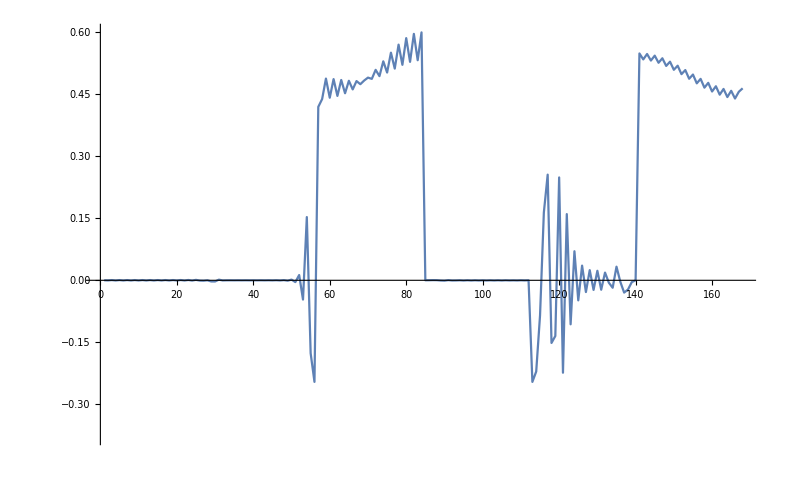

```mathematica
ListPlot[realvec[10],PlotRange->All,Joined->True]
```

```mathematica
(* read in matrices from Fortran *)
```

```mathematica
ClearAll["Global`*"]
SetDirectory["~/Desktop/Fortran/EV_spectral/M/"];
```

```mathematica
MatR=ReadList["graphRHS.txt",Number];
MatRi=ReadList["graphRHSimag.txt",Number];
MatL=ReadList["graphLHS.txt",Number];
MatLi=ReadList["graphLHSimag.txt",Number];
```

```mathematica
Len=Sqrt[Length[MatR]];
```

```mathematica
NMatR={};
NMatRi={};
NMatL={};
NMatLi={};
```

```mathematica
Do[
AppendTo[NMatR,Table[MatR[[i+(j-1)*Len]],{i,1,Len}]];
AppendTo[NMatRi,Table[MatRi[[i+(j-1)*Len]],{i,1,Len}]];
AppendTo[NMatL,Table[MatL[[i+(j-1)*Len]],{i,1,Len}]];
AppendTo[NMatLi,Table[MatLi[[i+(j-1)*Len]],{i,1,Len}]];
,{j,1,Len}]
```

```mathematica
NMatL//MatrixForm;
```

```mathematica
LHSMat=NMatL+I*NMatLi;
RHSMat=NMatR+I*NMatRi;
```

```mathematica
Sort[Re[Eigenvalues[{LHSMat,RHSMat}]]]
```

{-134587.,-83424.6,-23812.9,-22923.1,-10328.1,-10099.7,-6024.92,-5733.34,-4438.92,-4029.87,-3895.38,-3542.9,-3080.18,-2848.37,-2511.21,-2228.19,-1959.27,-1725.99,-1549.46,-1539.55,-1371.65,-1177.21,-987.566,-819.54,-711.241,-709.058,-617.24,-505.058,-468.301,-448.556,-362.704,-332.211,-319.637,-282.774,-258.068,-239.883,-216.912,-191.963,-169.723,-154.808,-138.041,-118.311,-100.467,-88.2743,-76.6481,-62.3769,-49.3748,-40.2677,-33.1175,-24.2326,-16.3343,-10.8931,-7.479,-3.81453,-1.12235,-0.00223658,1.86523×10^-11,4.53962×10^12,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}